```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
ZPlot[U_,V_,{{umin_,umax_,ustep_},{vmin_,vmax_,vstep_},plotRange_}]:=Module[
{XXXLines,YYYLines},
YYYLines=Table[
ParametricPlot[{U[u,v ],V[u,v ]},
{u,umin,umax},ColorFunction->(RGBColor[#3,0,0]&)],
{v,vmin,vmax,vstep}
];
XXXLines=Table[
ParametricPlot[{U[u,v ],V[u,v ]},
{v,vmin,vmax},ColorFunction->(RGBColor[0,#3,0]&)],
{u,umin,umax,ustep}];
Show[
YYYLines~Join~XXXLines,
ImageSize->{600,600},
PlotRange->{{-plotRange,plotRange},{-plotRange,plotRange}},Axes->True,AxesStyle->{Red,Green}
]
];
{{umin,umax,ustep},{vmin,vmax,vstep},plotRange}={{-3,3,0.5},{-3,3,0.5},10};

Main[k_,l_]:=Module[{Fn,U,V},
Fn[z_]:=z^(k+l I);

U[x_,y_]:=Re[Fn[y+x I]];
V[x_,y_]:=Im[Fn[y+x I]];
Show[

ZPlot[U,V,{{umin,umax,ustep},{vmin,vmax,vstep},plotRange}],
ComplexVectorPlot[Fn[z],{z,-(plotRange+plotRange I),plotRange+plotRange I}],

ImageSize->{600,600},
PlotRange->{{-plotRange,plotRange},{-plotRange,plotRange}},Axes->True,AxesStyle->{Red,Green}
]

];



Manipulate[Main[k,l],{{k,1},-5,5,0.05},{{l,1},-5,5,0.05}]
```

0.5

{{x^4-6 x^2 y^2+y^4,4 x y (x^2-y^2)},x^4 y-2 x^2 y^3+y^5/5,x^4 y-2 x^2 y^3}

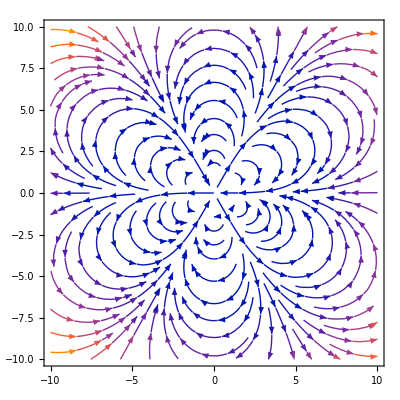
{-Graphics3D-,-Graphics-}

```mathematica
c=Simplify[(x+y I)^(4), {Element[x, Reals],Element[y, Reals]}];
zz=Simplify[{Re[c],Im[c]}//FunctionExpand,{Element[x, Reals],Element[y, Reals]}];

z1=Integrate[zz[[1]],y]//Simplify//Expand;
z2=Integrate[zz[[2]],x]//Simplify//Expand;
{zz,z1,z2}
{Plot3D[{z1},{x,-10,10},{y,-10,10}],
StreamPlot[-zz/.{x->X,y->Y},{X,-10,10},{Y,-10,10},StreamPoints->200]}
```